```mathematica
(*
Зуев В., гр. 13632/2;
Вариант 10;
*)
(*Task 1. Simplifying equation*)
Clear[x];
```

```mathematica
FullSimplify[7*Sin[x]-56*(Sin^3[x])+112*(Sin^5[x])-64*(Sin^7[x])]
```

-8 (7 Sin^(3[x])-14 Sin^(5[x])+8 Sin^(7[x]))+7 Sin[x]

```mathematica
(*Task 2. Calculating derivative*)
D[(x*∏_(k=0)^x (Cos[x/2^k])), x]
Clear[x];
(*another method (just to ensure everything's OK)*)
f[x_]:=x*∏_(k=0)^x (Cos[x/2^k]);
f'[x]
```

x ∂_x ∏_(k=0)^x Cos[2^-k x]+∏_(k=0)^x Cos[2^-k x]

x ∂_x ∏_(k=0)^x Cos[2^-k x]+∏_(k=0)^x Cos[2^-k x]

```mathematica
(*Task 3. Calculating limit*)
Clear[n];
Limit[(n^2-n^x)/(x-2),x->2]
Clear[x]; Clear[n];
```

-n^2 Log[n]

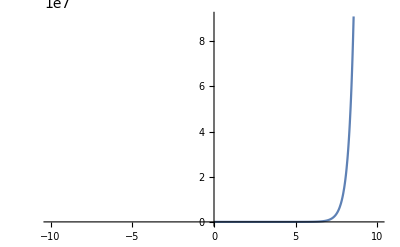

{0.692201,{x→0.367879}}

```mathematica
(*Task 4. Defining extremal points' coordinates*)
Plot[{x^x}, {x,-10,10}, PlotLegends -> "Expressions"]
FindMinimum[{Re[x^x], x ≥-100, x ≤100}, {x}]
```

```mathematica
(*Task 5. Solving linear equations system*)
m = {{12.4, -0.56,4.2}, {-0.65, 4.4,1.5}, {1.5,2.1 ,2.8}};
LinearSolve[m,{6.3, 1.5, 1.7}]
```

{0.519507,0.410512,0.0209514}

```mathematica
(*Task 5.2. Solving system of quad equations*)
```

```mathematica
Clear[x1,x2];
Solve[2x1*(x2)^2-4x2-7.5==0 && x1^2-3x1*x2+4.5==0,{x1,x2}]
Clear[x1,x2];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→-1.40174-3.07964 ⅈ,x2→-0.650895-0.623067 ⅈ},{x1→-1.40174+3.07964 ⅈ,x2→-0.650895+0.623067 ⅈ},{x1→-0.196523,x2→-7.69821},{x1→3.,x2→1.5}}